#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.8)^(-9);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-nod/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-nod/results

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

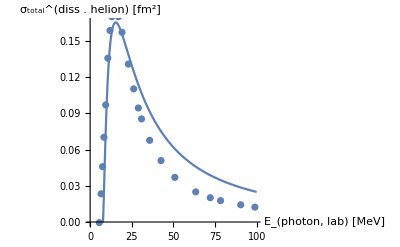

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Re[Eigensystem[norm]],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,0.2];
```

min/max: {3.22416×10^-13,116.902}

(min/max) discarded elements: 1881 {3.22416×10^-13,0.199403}

#### The real calculation

Set a sensible cut-off

min/max: {3.22416×10^-13,116.902}

(min/max) discarded elements: 47 {3.22416×10^-13,4.75172×10^-10}

B(^3He) = -7.38619

Dim_full^helion = 2304=^!2304   ;     Dim_(non - singular)^helion = 2257

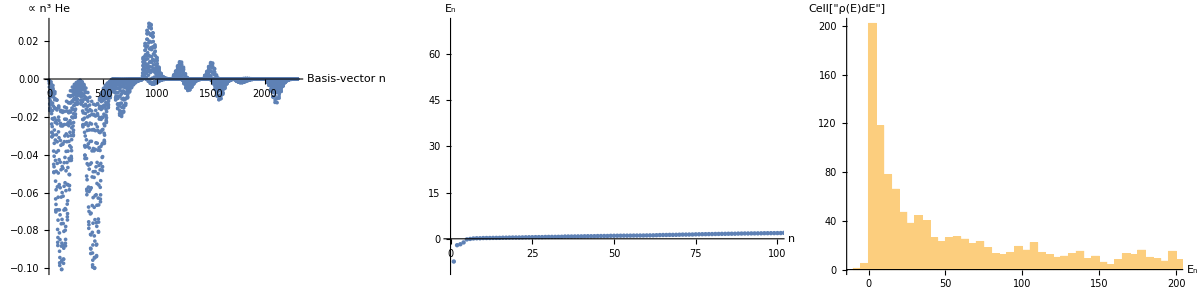

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];

orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0=orderedEVSYHe3[[1,1]];v0=orderedEVSYHe3[[1,2]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[He3Nmh].v0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,AxesLabel->{"Basis-vector n"," ∝ n^3 He"},ImageSize->Large],
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,70}},AxesLabel->{"n"," E_n"},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E_n","Cell["ρ(E)dE",ExpressionUUID->"cf919011-cdda-4cf7-9d6a-392ca1d5a758"]"}]
}}]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = {3744,2880}

min/max: {-1.44448×10^-9,120.518}

(min/max) discarded elements: 1388 {-1.44448×10^-9,4.98682×10^-10}

J=0.5:  E_0=-6.91125×10^-13

min/max: {-1.16132×10^-14,162.686}

(min/max) discarded elements: 732 {-1.16132×10^-14,4.95131×10^-10}

J=1.5:  E_0=0.0441741

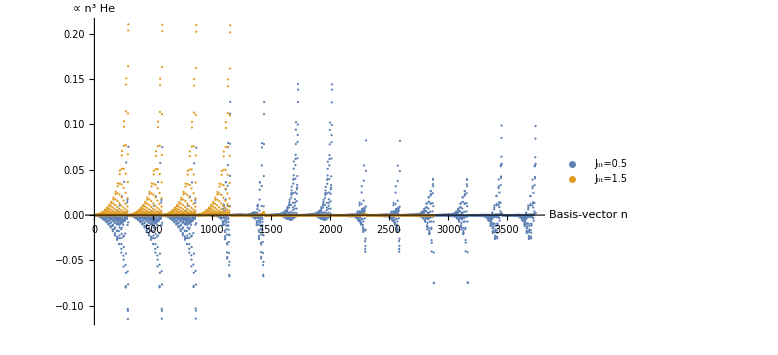
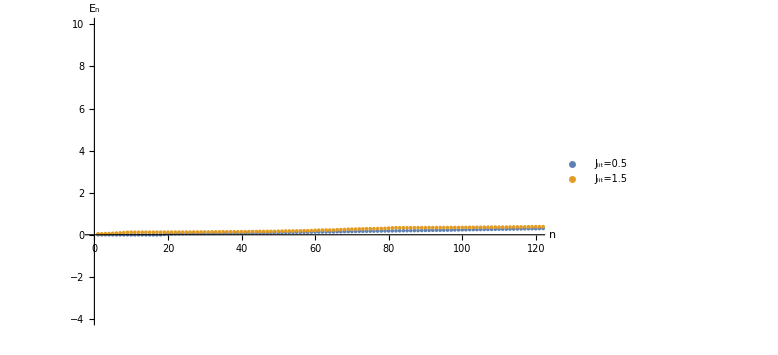
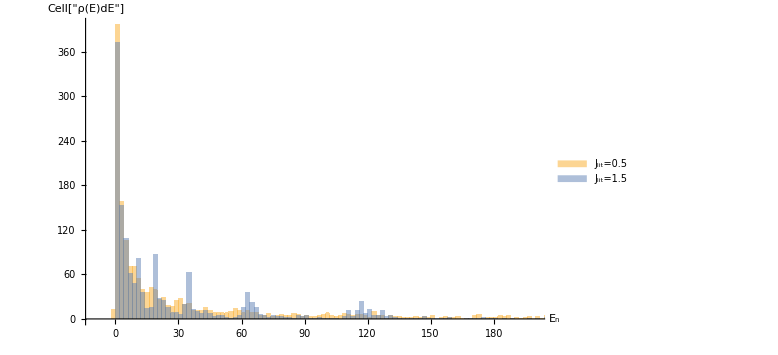
-Graphics- | -Graphics- | -Graphics-

```mathematica
LitNmhis={};
LitEVs={};
fullv0l={};
dE=2.;
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
orderedEVSYOut=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0l=orderedEVSYOut[[1,1]];v0l=orderedEVSYOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Normalize[Transpose[LitNmh].v0l]];
AppendTo[LitEVs,orderedEVSYOut[[All,1]]];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{"Basis-vector n"," ∝ n^3 He"},ImageSize->Large,PlotLegends->lege],
ListPlot[LitEVs,PlotRange->{{0,120},{-4,10}},AxesLabel->{"n"," E_n"},ImageSize->Large,PlotLegends->lege],
Histogram[LitEVs,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E_n","Cell["ρ(E)dE",ExpressionUUID->"0684a468-be60-4b73-8dc2-82b8173af1c0"]"},ChartLegends->lege]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

(*CouplingBlocks={};
Do[
Print["(Lm_LJ_0m_I_n-m_l|I_nm_I_n) = (",multipolarity,mL,J0,mIn-mL,"|",Subscript[I, n][[nj]],mIn,")"];
If[Sign[mIn]>=0,mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],2,"0"],mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],3,"0"]];
If[Sign[mL]>=0,mMUL=StringPadRight[StringDelete[ToString[mL],"."],2,"0"],mMUL=StringPadRight[StringDelete[ToString[mL],"."],3,"0"]];

files="./"<>ToString[#]<>"_S_"<>JLIT<>"_"<>mJLIT<>"_"<>mMUL<>".lit"&/@ks;
(*Print[files]*)
inhomos=readREAL8list[#]&/@files;
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[He3BasisDim+1;;,;;He3BasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
coupl=ClebschGordan[{multipolarity,mL},{J0,mIn-mL},{Subscript[I, n][[nj]],mIn}];
(*Print["⟨",multipolarity,mL,J0,mIn-mL,"|",Subscript[I, n][[nj]],mIn,"⟩ =  ",coupl];*)
(*Print[ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],He3BasisDim}]//MatrixForm];*)
AppendTo[CouplingBlocks,coupl ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],He3BasisDim}]];
(*Clear[CouplingBloxx];*)
,{mL,mM}
];
AppendTo[CouplingBlock,{mIn,Total[CouplingBlocks]}];
*)

tmp =BinaryReadList["InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
test=ArrayReshape[tmp,{OutDim,He3BasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];

(*If[Select[Flatten[test],Chop[#,10^-8]==0&]=={},
If[Select[Flatten[Total[CouplingBlocks]/test],Chop[#-1.0,10^-7]≠0.&]≠{},
Print["m_I_n=",mIn,"  : ",Flatten[Total[CouplingBlocks]/test]]//MatrixForm];
];*)

(*Print["m_I_n=",mIn,"  : ",Total[CouplingBlocks]//MatrixForm];*)
,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Dim(⟨ψ|ο̂|helion⟩) = {2}

Dim(⟨ψ|Ĥ|ψ⟩) = {2}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {2}

#### Analysis of RHS

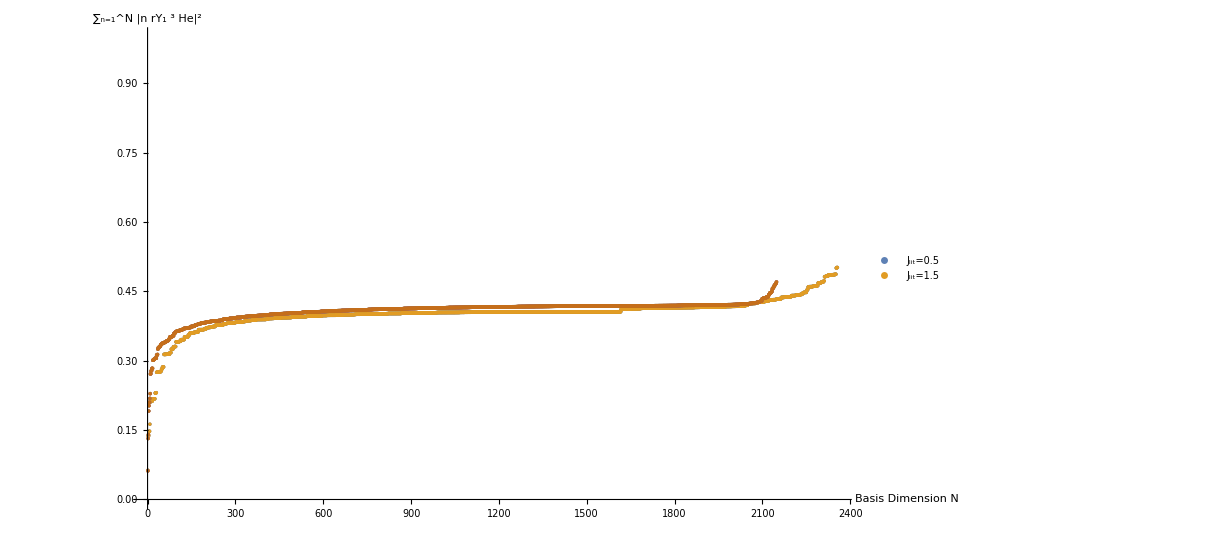

```mathematica
OμRHS=normreg[thresholdLIT,He3Norm];
{λsHe,trfHe}=Re[Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};
Do[
Do[
OμLHS=normreg[thresholdLIT,LitNorm[[nj]]];
{λfinal,trfLit}=Re[Eigensystem[(Transpose[OμLHS].LitHam[[nj]]).OμLHS]];
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomo,(Transpose[OμLHS].(tmp.OμRHS)).evgs];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
mm=1;

inhomonorms=Table[Norm[#[[;;n]]],{n,Length[#]}]&/@inhomo;
ListPlot[inhomonorms,AxesLabel->{"Basis Dimension N","∑_(n=1)^N |n rY_1^3 He|^2"},PlotLegends->lege,ImageSize->ImgSize,PlotRange->{Automatic,{0,1}}]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=4.0;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];

Clear[decompose];
decompose[threshold_,He3Norm_,He3Ham_,LITNorm_,LITHam_,LITYD_]:= Block[{OμRHS,λsD,trfD,OμLHS,λfinal,trfLit,inhomo,egs,evgs},
OμRHS=normreg[threshold,He3Norm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS];
egs=Min[λsD];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[threshold,LITNorm];

{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

Print["E_0( th=",N[threshold]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

inhomo=(Transpose[OμLHS].(LITYD.OμRHS)).evgs;
{λfinal,(trfLit.inhomo)^2,egs}
];

Clear[litcomp];
litcomp[threshold_,He3Norm_,He3Ham_,LITNorm_,LITHam_,LITYD_]:=
Block[
{λscf=decompose[threshold,He3Norm,He3Ham,LITNorm,LITHam,LITYD]},
egrnd=λscf[[3]];
tmpp=Transpose[λscf[[;;2]]];
Plus@@((#[[2]]/(Abs[#[[1]]-egrnd-σRe]^2+σI^2))&/@tmpp)
];
```

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0( th=5.00249×10^-10 ) = -7.38619    dim(He3,LIT) = {2257}{2356}

E_0( th=5.00249×10^-10 ) = -7.38619    dim(He3,LIT) = {2257}{2148}

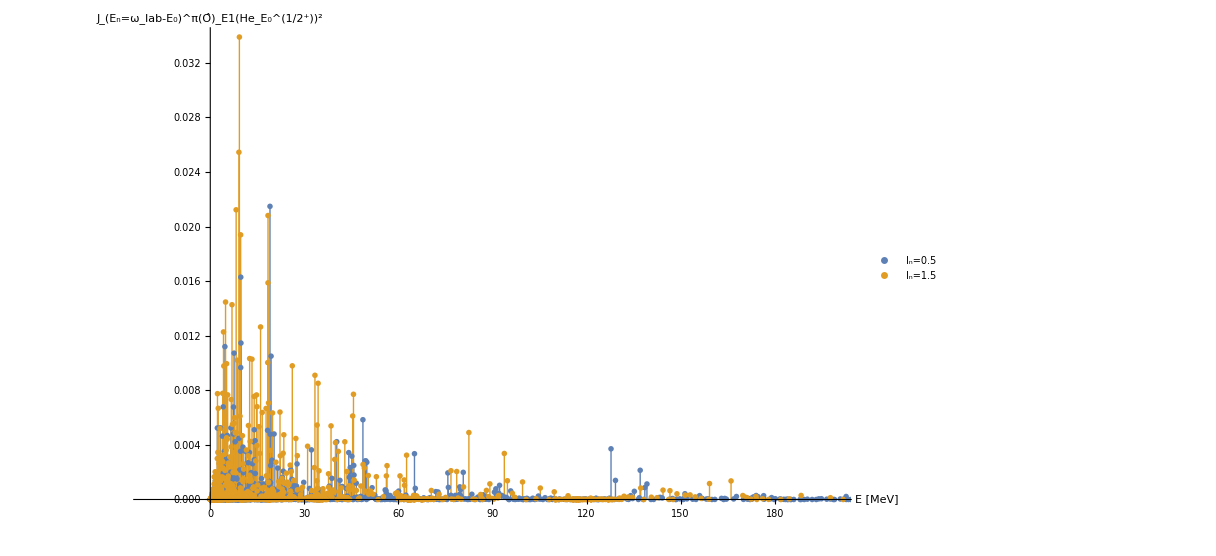
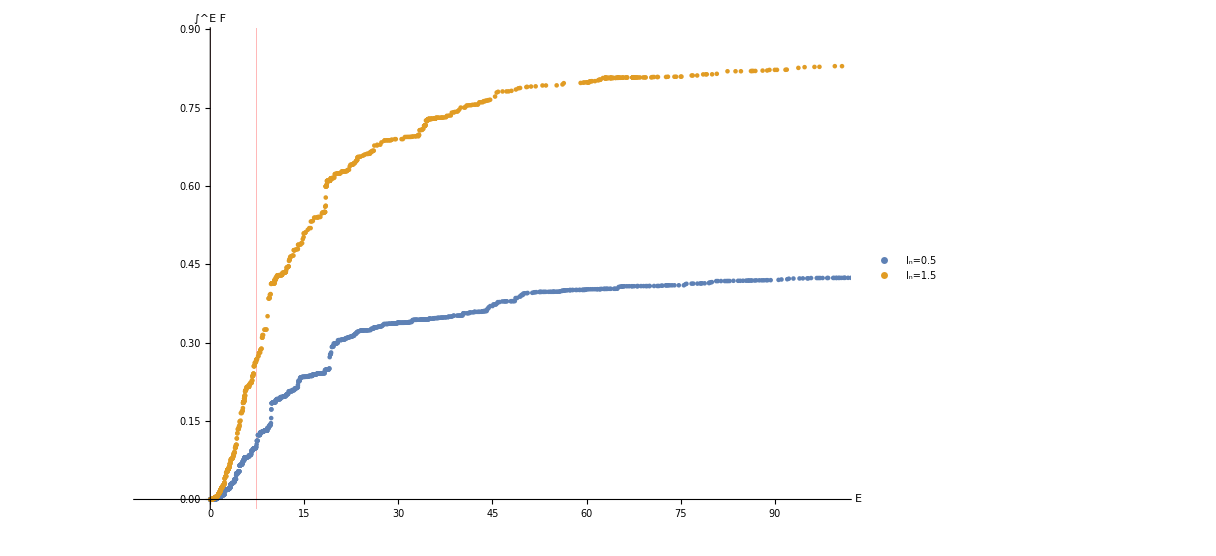

```mathematica
Clear[es,μ,transf];
lpsis={};CumStrengths={};

es=Re[Eigensystem[He3Norm]];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresholdLIT&]];
OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];

leg={};

Do[
lpsi={};
esl=Re[Eigensystem[LitNorm[[nj]]]];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresholdLIT&]];
OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);
{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].(LitHam[[nj]])).OμLHS];

Print["E_0( th=",N[thresholdLIT]," ) = ",egs,"    dim(He3,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

tmpl=0;

Do[
inhomo=(Transpose[OμLHS].(CouplingBlockj[[nj]][[mm]][[2]].OμRHS)).(evgs);
AppendTo[lpsi,Transpose[{λfinal(*+Abs[egs]*),(trfLit.inhomo)^2}]];
tmpl = tmpl + (trfLit.inhomo)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsis,Re[Transpose[{λfinal,tmpl}]]];
AppendTo[CumStrengths,Re[Transpose[{Sort[lpsis[[nj]]][[All,1]],Accumulate[Sort[lpsis[[nj]]][[All,2]]]}]]];

AppendTo[leg,"I_n="<>ToString[Subscript[I, n][[nj]]]];

(*AppendTo[lpsis,Flatten[lpsi,1]];*)

,{nj,Range[1,Length[Subscript[I, n]]]}
]


plote3=Grid[{{
ListPlot[lpsis,Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",18],Style["Cell[TextData[Cell[BoxData[RowBox[{\nTemplateBox[{SubsuperscriptBox[\"J\", RowBox[{SubscriptBox[\"E\", \"n\"], \"=\", RowBox[{SubscriptBox[\"ω\", \"lab\"], \"-\", SubscriptBox[\"E\", \"0\"]}]}], \"π\"]},\"Bra\"], \nSubscriptBox[\nOverscriptBox[\"O\", \"^\"], \"E1\"], \nSuperscriptBox[\nTemplateBox[{SubsuperscriptBox[\"He\", SubscriptBox[\"E\", \"0\"], RowBox[{\"1\", \"/\", SuperscriptBox[\"2\", \"+\"]}]]},\"Ket\"], \"2\"]}]]]]]",18]},PlotStyle->{},PlotLegends->leg,ImageSize->ImgSize]
},{
ListPlot[CumStrengths,Joined->False,ImageSize->ImgSize,PlotRange->{{-10,100},Automatic},PlotLegends->leg,GridLines->{{{Abs[e0],Red},{Abs[e0l],Red}},None},AxesLabel->{Style["E",18],Style["Cell[TextData[{\nCell[BoxData[FormBox[\nOverscriptBox[\"∫\", \"E\"], TraditionalForm]]],\n\"F\"\n}]]",18]}]
}}]
(*Save[tmpDir<>"/lpsis.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],lpsis]
Save[tmpDir<>"/CumStrength.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],CumStrengths]
Export["delta_strength_function_helion.pdf",plote3,"PDF","AllowRasterization"->False]*)
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengths,LocalObject["CumHelionStrengths"]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumHelionStrengths]

E_final=E_0+ω
for disintegration, the photon energy ω is s.t.: ω>E_0-E_1
with E_1being the lowest threshold which can be reached with the perturbation. Here, it is equivalent to the smallest Eigenvalue of the Hamiltonian in the LHS Hilbert space.

{(t^2 (0.503305 t^2+62.1154 t+8.31891))/(1. t^4+158.652 t^3+589.143 t^2+18160.6 t+0.0476662),(t^2 (0.885099 t^2+0.308269 t+0.223384))/(1. t^4+6.47695 t^3+55.633 t^2+158.206 t+0.000485717)}

{Piecewise[{{(17.7349 t^6-209.559 t^5+55922.2 t^4+575302. t^3-3.08494×10^7 t^2+2.72203×10^8 t-7.24067×10^8)/((-1. t^4-129.107 t^3+2599.02 t^2-33811.9 t+162951.)^2), t≥7.38619}, {0, True}}],Piecewise[{{(5.42447 t^6-143.8 t^5+1285.92 t^4-3235.36 t^3-11928.3 t^2+57515.3 t-17214.4)/((1. t^4-23.2445 t^3+242.517 t^2-1236.69 t+2287.11)^2), t≥7.43037}, {0, True}}]}

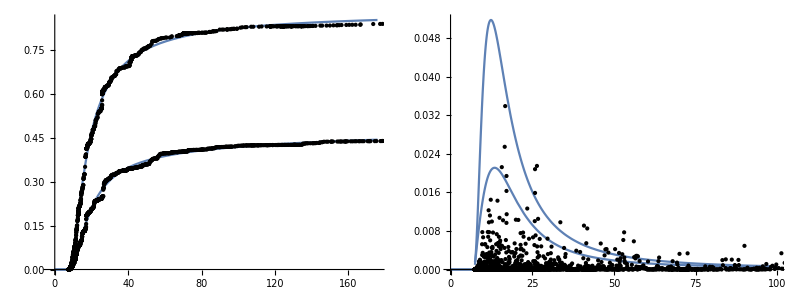

```mathematica
data=CumStrengths;
offsets=Min[#[[All,1]]]&/@data;
dataShifted=Transpose[{#[[All,1]]-#[[All,1]][[1]],#[[All,2]]}]&/@CumStrengths;
data=dataShifted;
ordnum=4;orddenom=ordnum-1;
coffs={Array[cnum,ordnum],Array[cdenom,orddenom+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.0001,0.2},Length[Flatten[coffs]]]}];

(*num=Sum[coffs[[1]][[n]] (t)^n,{n,ordnum}]&/@Range[Length[data]];
denom=1+Sum[coffs[[2]][[n]] (t)^n,{n,orddenom}]&/@Range[Length[data]];*)
num=Sum[coffs[[1]][[n]] (t)^n,{n,2,ordnum}]&/@offsets;
denom=1+coffs[[2]][[-1]] (t)^ordnum+Sum[coffs[[2]][[n]] (t)^n,{n,orddenom}]&/@offsets;

model=num/denom;
constr=#>10.2^(-2)&/@Flatten[coffs];(*10.1^2>#>10.2^(-2)&/@Flatten[coffs];*)
constraints=Union[constr,{Abs[coffs[[1]][[-1]]/coffs[[2]][[-1]]-data[[#]][[-1]][[2]]]<10.^(-9)}]&/@Range[Length[data]];

wgts=Abs[Flatten[Join[{Differences[data[[#]]][[All,2]][[1]],Differences[data[[#]]][[All,2]]}]]&/@Range[Length[data]]];
splitPoint=10;
origFac=112.;
tailFac=21.;

wgt2=Join[origFac #[[;;splitPoint]],#[[1+splitPoint;;-splitPoint]],tailFac #[[-splitPoint+1;;]]]&/@wgts;

optPOSsol=
NonlinearModelFit[dataShifted[[#]],{model[[#]],constraints[[#]]},inicoffs,t,Weights->wgt2[[#]],MaxIterations->5500]&/@Range[Length[data]];

CumFit[ee_]:=Piecewise[ {{optPOSsol[[#]][ee-Abs[e0-offsets[[#]]]],ee≥Abs[e0-offsets[[#]]]},{0,ee<Abs[e0-offsets[[#]]]}}]&/@Range[Length[optPOSsol]]
StC[em_]:=Piecewise[{{D[optPOSsol[[#]][t],t]/.t->(em-Abs[e0-offsets[[#]]]),em≥Abs[e0-offsets[[#]]]},{0,em<Abs[e0-offsets[[#]]]}}]&/@Range[Length[data]]

Simplify[#[t]]&/@optPOSsol//TraditionalForm
Simplify[#]&/@StC[t]//TraditionalForm

percPlot =0.01;
Grid[{{
Plot[CumFit[t][[#]]&/@Range[Length[data]],{t,Min[offsets],percPlot Max[#[[All,1]][[-1]]&/@data]},Epilog->{PointSize[Small],Point[Transpose[{data[[#]][[All,1]]+Abs[e0-offsets[[#]]],data[[#]][[All,2]]}]]&/@Range[Length[data]]},PlotRange->{{-2.3,percPlot Max[#[[All,1]][[-1]]&/@data]},{0,Automatic}},ImageSize->ImgSize],
Plot[StC[e2],{e2,Min[offsets],100},Epilog->Map[Point,Transpose[{lpsis[[#]][[All,1]]+Abs[e0-offsets[[#]]],lpsis[[#]][[All,2]]}]&/@Range[Length[data]]],PlotRange->Full,ImageSize->ImgSize]
}}]
```

#### σ_tot=(2π)^2 α·E_γ ∑_(J,M) JM OverHat[E1](J_0 m_0)^2

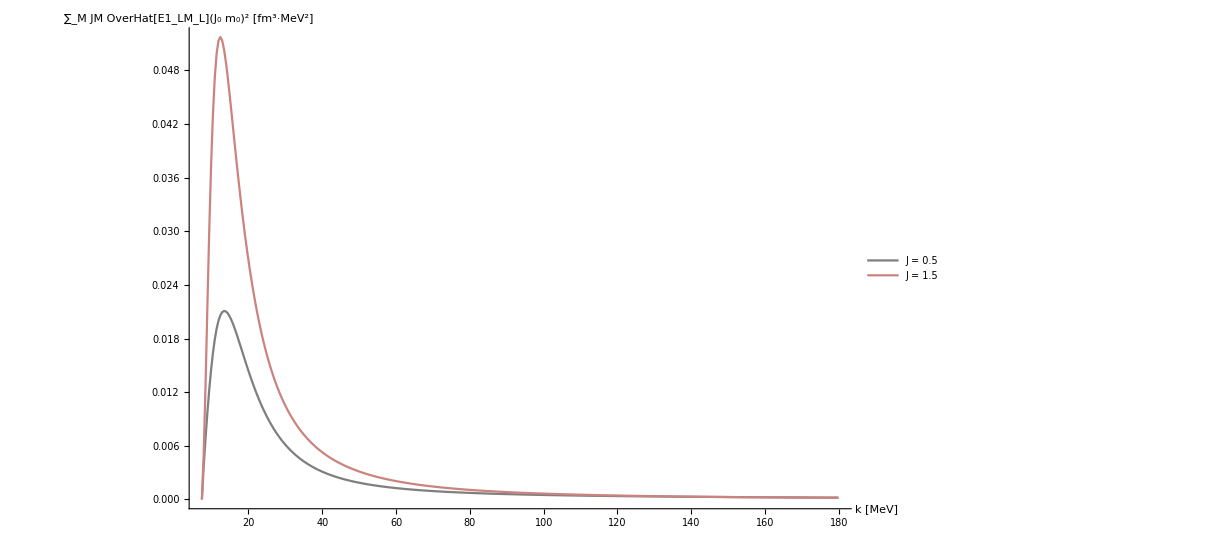
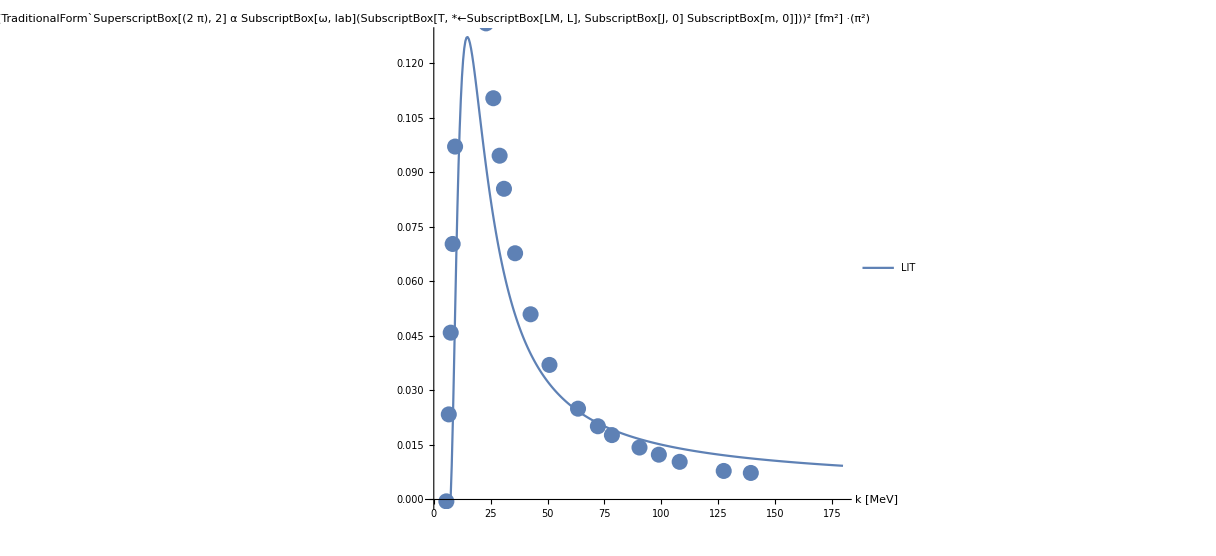
-Graphics- | -Graphics-

```mathematica
Clear[ee,e2];
k0=0.001;k1=180;dK=0.5;
Subscript[k, lab]=Range[Abs[e0],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;

labelj=("J = "<>ToString[#])&/@Subscript[I, n];
responseListJ=StC[t];
strengthfunctionList=Table[Table[(responseListJ[[nJ]]/.t->ee)/.ee->kmag,{kmag,Subscript[k, lab]}],{nJ,Range[1,Length[Subscript[I, n]]]}];

z=List[];

For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,(
atmp=ListLinePlot[strengthfunctionList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","FormBox[RowBox[{UnderscriptBox[\"∑\", \"M\"], RowBox[{TemplateBox[{\"JM\"},\"Bra\"], OverscriptBox[SubscriptBox[\"E1\", SubscriptBox[\"LM\", \"L\"]], \"^\"], SuperscriptBox[TemplateBox[{RowBox[{SubscriptBox[\"J\", \"0\"], SubscriptBox[\"m\", \"0\"]}]},\"Ket\"], \"2\"]}]}],TraditionalForm] [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];

Tsquared[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,
compo=strengthfunctionList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
ampli+=compo;
];
];];
Return[ampli]
]
fudgi=Pi^2;

kinfac=fudgi (2 Pi)^2 Subscript[α, fine] (Subscript[k, lab])/hbarc;

DissCross[Mf_,Mi_,λf_,kinfac_]:=kinfac Tsquared[Mf,Mi,λf,θ];
lf=1;

Grid[{{
Show[z,PlotRange->All],
Show[ListPlot[Re[DissCross[Jf,Ji,lf,kinfac]],PlotRange->{Automatic,{0,Full}},LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`SuperscriptBox[(2  π), 2] α SubscriptBox[ω, lab](SubscriptBox[T, *←SubscriptBox[LM, L], SubscriptBox[J, 0] SubscriptBox[m, 0]]))^2 [fm^2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotLegends->{"LIT"}],
ListPlot[He3DataFm2,PlotLegends->"σ_tot data"]]
}}]
```

d^5 σ_(He→npp)=(2π)^2 α ω_lab ∑|p_1 q_1Ô(ω)He|^2 d^3(p_1,q_1)δ(p_1^2+3/4 q_1^2-ω)

```mathematica
Clear[solu,wcm,wlab,wcem]
solu=Solve[wcm==wlab (1+2 wlab/mdeu)^(-1/2),wlab];
wl=Simplify[wlab/.solu[[2]]]

kcross=0.5 Sqrt[(wcem+e0-2 mn)(wcem+e0+2 mn)]
```

(wcm^2+√(wcm^2 (mdeu^2+wcm^2)))/mdeu

0.5 √((-1883.99+wcem) (1869.21+wcem))